```mathematica
<<DifferentialForms.m
```

SetDelayed::write: Tag TensorProduct in TensorProduct[single_] is Protected.

SetDelayed::write: Tag TensorProduct in vec[a_,x:{__}]⊗vec[b_,y:{__}]⊗C___ is Protected.

SetDelayed::write: Tag TensorProduct in head1_[a_,x:{__}]⊗head2_[b_,y:{__}]⊗C___ is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

Differential Forms package Version 4.0 by Frank Zizza

with additions by Ulrich Jentschura.  For information

about functions, Type ?DifferentialForms .

```mathematica
Laplace[f[r], t[r,r]+r^2 t[θ,θ]]//FullSimplify
```

-(f'[r]+r f''[r])/r

```mathematica
LapPhi=Laplace[f[r], 1/(1-K r^2)t[r,r]+r^2 t[θ,θ]+r^2 Sin[θ]^2 t[ϕ, ϕ ]]//FullSimplify
```

((-4+6 K r^2+r^3) f'[r])/(2 r)+(-1+K r^2) f''[r]

## Solving Laplace Equation in a Closed Universe

```mathematica
LapPhiClosed=-Laplace[f[χ], (t[χ, χ]+Sin[χ]^2 t[θ,θ]+Sin[χ]^2 Sin[θ]^2 t[ϕ, ϕ ])]//FullSimplify
```

2 Cot[χ] f'[χ]+f''[χ]

```mathematica
ρ[x_]:=Piecewise[{{Subscript[ρ, 0], x<R}, {0, x>R}}]
```

```mathematica
DSolve[{LapPhiClosed==κ ρ[χ]}, f[χ], {χ, 0,π}]//FullSimplify
```

{{f[χ]→1/2 (-2 ⅈ C[1]+C[2]+(2 C[1]-ⅈ C[2]) Cot[χ]+κ ρ_0 (-χ Cot[χ]+((-R+χ) Cot[χ]+Cos[R] Csc[χ] Sin[R-χ]) UnitStep[-R+χ]))}}

```mathematica
SolClosed=f[χ]/.(%//First)
```

1/2 (-2 ⅈ C[1]+C[2]+(2 C[1]-ⅈ C[2]) Cot[χ]+κ ρ_0 (-χ Cot[χ]+((-R+χ) Cot[χ]+Cos[R] Csc[χ] Sin[R-χ]) UnitStep[-R+χ]))

```mathematica
SolClosed/.χ->R//FullSimplify
```

1/2 (-2 ⅈ C[1]+C[2]+2 C[1] Cot[R]-ⅈ C[2] Cot[R]-R κ Cot[R] ρ_0)

```mathematica
Assuming[R>π/2,Limit[SolClosed,χ->π/2]]
```

1/2 (-2 ⅈ C[1]+C[2])

```mathematica
Assuming[R<π/2,Limit[SolClosed,χ->π/2]]
```

1/2 (-2 ⅈ C[1]+C[2]-κ Cos[R]^2 ρ_0)

```mathematica
Assuming[χ<R, SolClosed//FullSimplify]
```

1/2 (-2 ⅈ C[1]+C[2]+2 C[1] Cot[χ]-ⅈ C[2] Cot[χ]-κ χ Cot[χ] ρ_0)

```mathematica
Assuming[χ>R, SolClosed//FullSimplify]
```

1/2 (-2 ⅈ C[1]+C[2]+(2 C[1]-ⅈ C[2]) Cot[χ]+κ (-R Cot[χ]+Cos[R] Csc[χ] Sin[R-χ]) ρ_0)

```mathematica
UniqSolClosed=SolClosed/.{C[1]->I/2 C[2]}//FullSimplify
```

C[2]+1/2 κ ρ_0 (-χ Cot[χ]+((-R+χ) Cot[χ]+Cos[R] Csc[χ] Sin[R-χ]) UnitStep[-R+χ])

```mathematica
Assuming[χ<R, UniqSolClosed//FullSimplify]
```

C[2]-1/2 κ χ Cot[χ] ρ_0

```mathematica
Assuming[χ>R, UniqSolClosed//FullSimplify]
```

C[2]+1/2 κ (-R Cot[χ]+Cos[R] Csc[χ] Sin[R-χ]) ρ_0

## Solving Laplace Equation in a Flat Universe

```mathematica
LapPhiFlat=-Laplace[f[χ], (t[χ, χ]+χ^2 t[θ,θ]+χ^2 Sin[θ]^2 t[ϕ, ϕ ])]//FullSimplify
```

(2 f'[χ])/χ+f''[χ]

```mathematica
ρ[x_]:=Piecewise[{{Subscript[ρ, 0], x<R}, {0, x>R}}]
```

```mathematica
DSolve[{LapPhiFlat==κ ρ[χ]}, f[χ], {χ, 0,Infinity}]//FullSimplify
```

{{f[χ]→C[2]+(-6 C[1]+κ ρ_0 (χ^3-(R-χ)^2 (2 R+χ) UnitStep[-R+χ]))/(6 χ)}}

```mathematica
SolFlat=f[χ]/.(%//First)
```

C[2]+(-6 C[1]+κ ρ_0 (χ^3-(R-χ)^2 (2 R+χ) UnitStep[-R+χ]))/(6 χ)

```mathematica
Limit[SolFlat,χ->Infinity]
```

C[2]+1/2 R^2 κ ρ_0

```mathematica
UniqSolFlat=(SolFlat/.{Solve[Limit[SolFlat,χ->Infinity]==0, C[2]]}//FullSimplify//First//First)/.C[1]->0
```

(κ ρ_0 (-3 R^2 χ+χ^3-(R-χ)^2 (2 R+χ) UnitStep[-R+χ]))/(6 χ)

```mathematica
Assuming[χ<R, UniqSolFlat//FullSimplify]
```

1/6 κ (-3 R^2+χ^2) ρ_0

```mathematica
Assuming[χ>R, UniqSolFlat//FullSimplify]
```

-(R^3 κ ρ_0)/(3 χ)

```mathematica
UniqSolFlat/.χ->R//FullSimplify
```

-1/3 R^2 κ ρ_0

## Plot the functions

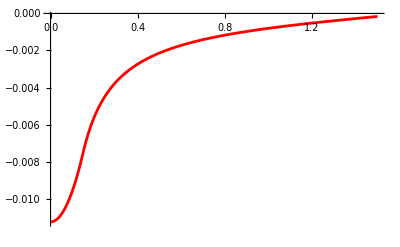

```mathematica
rr=0.15;
 Plot[(UniqSolClosed/.C[2]->(1/2)(1-rr^2)Subscript[ρ, 0] κ)/(Subscript[ρ, 0] κ)/.R->rr, {χ, 0, Min[10*rr, π]}, PlotStyle->Red, PlotRange->Full]
```

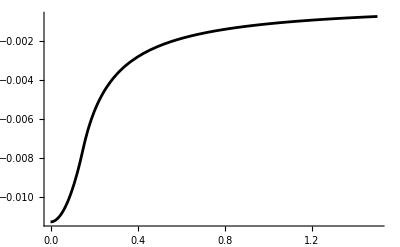

```mathematica
Plot[ UniqSolFlat/(Subscript[ρ, 0] κ)/.R->rr, {χ, 0, Min[10*rr, π]}, PlotStyle->Black]
```

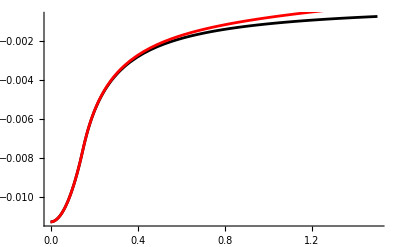

```mathematica
Show[%, %%]
```